```mathematica
(*
e[x]_here = e[1][x]_{Lagrangian approach}
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ϵ[1]=1;
```

```mathematica
ass={ψ[x]∈Reals,ν[x]>0};
```

```mathematica
e[x_]:=ν[x]{Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ν[x] ψ'[x]}}

```mathematica
b[x_]:={{-ν[x] ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-ψ'[x]/(2 ν[x])

```mathematica
H[x_]:=-ψ'[x]/(2 ν[x])
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:=ResourceFunction["ChristoffelSymbol"][g[x],{x}] //FullSimplify
```

```mathematica
Γ[x]
```

{{{ν'[x]/ν[x]}}}

```mathematica
(* \Nabla_k f_i*)
```

```mathematica
Nablaf[f_][i_,k_][x_]:=Derivative[ϵ[k]][f[i]][x]-Sum[f[j][x] Γ[x][[j,i,k]],{j,1,1}]
```

```mathematica
dH[1][x_]:=H'[x]
```

```mathematica
FullSimplify[Sum[gc[x][[i,j]]Nablaf[dH][i,j][x],{i,1,1},{j,1,1}],Assumptions->ass]
```

(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] ψ^(3)[x]))/(2 ν[x]^5)

```mathematica
NabNabH[x_]:=(-3 ν'[x]^2 ψ'[x]+3 ν[x] ν'[x] ψ''[x]+ν[x] (ψ'[x] ν''[x]-ν[x] Derivative[3][ψ][x]))/(2 ν[x]^5)
```

```mathematica
eqψ=FullSimplify[{2 κ(2H[x](H[x]^2-K[x])+NabNabH[x])-2 σ[x]H[x]==0},Assumptions->ass]
```

{2 ν[x] (ψ'[x] (ν[x]^3 σ[x]+κ ν''[x])+3 κ ν'[x] ψ''[x])==6 κ ν'[x]^2 ψ'[x]+κ ν[x]^2 (ψ'[x]^3+2 ψ^(3)[x])}

```mathematica
eqX={X1'[x]==ν[x] Cos[ψ[x]],X2'[x]==-ν[x] Sin[ψ[x]]}
```

{X1'[x]==Cos[ψ[x]] ν[x],X2'[x]==-Sin[ψ[x]] ν[x]}

```mathematica
bcs={ψ[xmin]==ψmin,ψ''[xmin]==ψppmin,ψ'[xmin]==ψpmin,X1[xmin]==X1min,X2[xmin]==X2min};
```

```mathematica
σ[x_]:=σc
(*fix the gauge*)
ν[x_]:=4
```

```mathematica
eqψ
```

{512 σc ψ'[x]==16 κ (ψ'[x]^3+2 ψ^(3)[x])}

```mathematica
(*parameters*)
```

```mathematica
κ=1;
σc=1;
xmin=1;
xmax=3;
ψmin=-1/2;
(*
	dψ/dx=dψ/ds * ds/dx = dψ/ds * ν;
	dψ/ds is gauge independent, while dψ/dx depends on the gauge;

	d^2ψ/dx^2 = d/dx(dψ/dx) = d/dx(dψ/ds * ν) = ν^2 * d^2ψ/ds^2 + dψ/ds * dν/dx;
*)
dψdsmin = -1;
ψpmin=dψdsmin ν[xmin];

d2ψds2min=25/10;
ψppmin=d2ψds2min ν[xmin]^2+ dψdsmin ν'[xmin];

X1min=0;
X2min=0;
```

```mathematica
s=NDSolve[Flatten[{eqψ,eqX,bcs}],{ψ,X1,X2},{x,xmin,xmax}]
```

{{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…]}}

```mathematica
X2[xmax]/.s
```

{-1.26975}

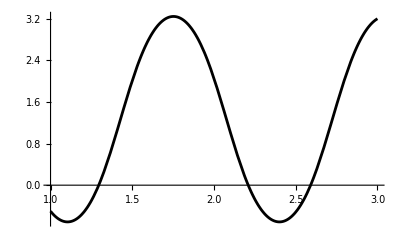

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Black]
```

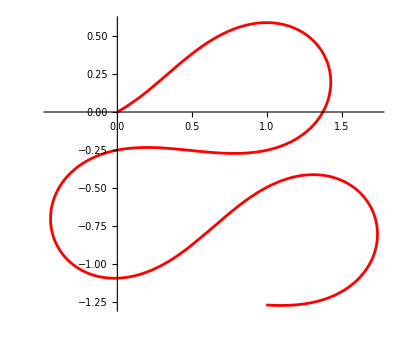

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Red]
```

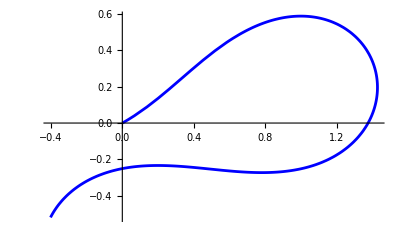
```mathematica
Show[-Graphics-,-Graphics-,PlotRange->Full]
```